# Homework 1

Name: Adel

ID: 201801454

## Problem 1

```mathematica
myfact[1]=1;
myfact[n_]:=n myfact[n-1];
myfact[7]==Factorial[7](*test*)

oddfact[1]=1;
oddfact[0]=1;
oddfact[n_]:=n*oddfact[n-2];
oddfact[8]==Factorial2[8](*test*)

mybio[n_,m_]:=myfact[n]/(myfact[m]*myfact[n-m]);

mybio[14,2]==Binomial[14,2](*test*)
```

True

True

True

## Problem 2

```mathematica
z=0.5;y=0.15;

NIntegrate[(1/Pi)* E^(y*Cos[x])*Cos[z*Sin[x]],{x,0,Pi}]-
BesselJ[0,Sqrt[z^2 - y^2]]
```

1.22125×10^-15

```mathematica
NIntegrate[1/Sqrt[6-u^2],{u,2,Sqrt[6]}]-ArcCot[N[Sqrt[2]]]
```

-1.41278×10^-8

```mathematica
(*effectively equall*)
```

## Problem 3

{x→2.29317}

2.29317

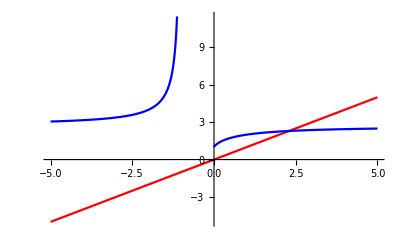

```mathematica
root=FindRoot[x==(1+1/x)^x,{x,1}]
sol=x/.root
Show[Plot[{x,(1+1/x)^x},{x,-5,5},PlotStyle->{Red,Blue}]]
```

## Problem 4

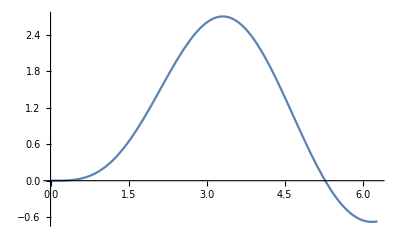

{x→5.27811}

```mathematica
Q[x_]:=If[0<=x&&x<=2Pi,(x-Sin[x])^(5/3) / x^(2/3)];
Plot[(5 (1-Cos[x]) (x-Sin[x])^(2/3))/(3 x^(2/3))-(2 (x-Sin[x])^(5/3))/(3 x^(5/3)),{x,0,2Pi}]

FindRoot[Q'[x],{x,4}]
(*choose x0 according to graph*)
```

```mathematica
N[(5.27811-Sin[5.27811])^(5/3) / 5.27811^(2/3) ]
```

6.75886

```mathematica
(* Ang = 5.2 rad, Q_max= 6.7*)
```

## Problem 5

{a→1065.44,b→0.104716,c→742.983,d→530.177}

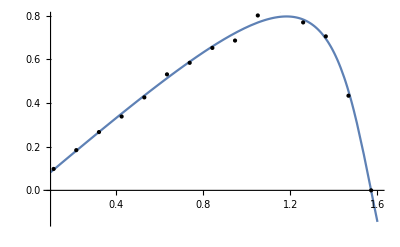

```mathematica
input={{0.01,0.0},{0.1141,0.09821},{0.2181, 0.1843},{0.3222, 0.2671},{0.4262, 0.3384},{0.5303, 0.426},{0.6343 ,0.5316},{0.7384, 0.5845},{0.8424, 0.6527},{0.9465, 0.6865},{1.051, 0.8015},{1.155, 0.8265},{1.259 ,0.7696},{1.363, 0.7057},{1.467,0.4338},{1.571,0}};

modelfunc=ArcTan[(a*Cot[x]*Sin[x]^2 -b*Cot[x])/(c+d*Cos[2x])];
fitfunction=FindFit[input,modelfunc,{a,b,c,d},x]
modelf=Function[{x},Evaluate[modelfunc/.fitfunction]];
Plot[modelf[x],{x,0.1,1.6},Epilog->Point[input]]
```

## Problem 6

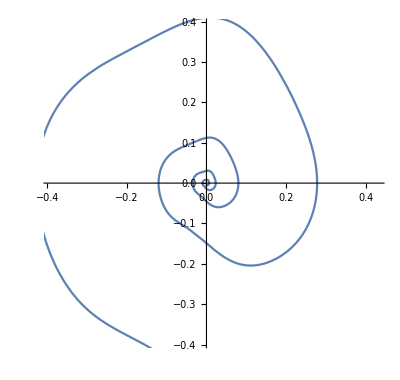

{{InterpolatingFunction[…],InterpolatingFunction[…]}}

```mathematica
γ=0.4; ε=0.16;w=0.97;
L=1+ε*Sin[w*t+9*Pi/8]^7;
s=NDSolve[{y1'[t]==y2[t],y2'[t]==-((2/L)*D[L,t]+γ*L)y2[t]-(1/L)Sin[y1[t]],y1[0]==-1,y2[0]==1},{y1,y2},{t,0,30}];
ParametricPlot[Evaluate[{y1[t],y2[t]}/.s],{t,0,30}]
y={y1,y2}/.s
```

## Problem 7

## Problem 8

## Problem 9

## Problem 10